Positive precompression

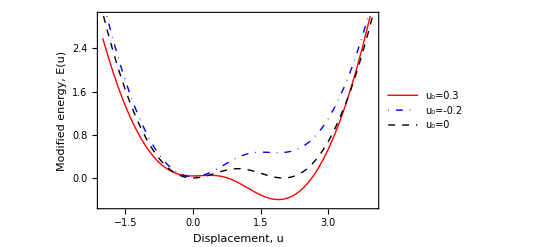

```mathematica
ψ[u_]=(√((1-u)^2+d^2)-√(1+d^2))^2;
uo=0.3;
u1=-0.2;
d=1;
Plot[{ψ[u+uo]-u ψ'[uo],ψ[u+u1]-u ψ'[u1],ψ[u]},{u,-2,4},PlotRange->{-0.5,3},Frame->True,PlotStyle->{Directive[Red,Thick],Directive[DotDashed,Blue,Thick],Directive[Dashed,Black,Thick]},FrameLabel->{"Displacement, u","Modified energy, E(u)"},PlotLegends->Placed[LineLegend[{Directive[Red,Thick],Directive[DotDashed,Blue,Thick],Directive[Dashed,Black,Thick]},{"u_0=0.3","u_0=-0.2","u_0=0"}],{Center,Top}],BaseStyle->{FontFamily->"Times",14}]
```

```mathematica
ψ'[uo]
```

0.221996

```mathematica
Solve[ψ'[u+uo]-ψ'[uo]==0]
```

{{u→-2.42131×10^-16},{u→0.78632},{u→1.98672}}

Negative precompression

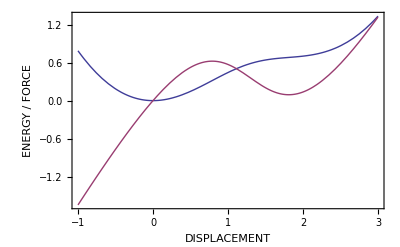

```mathematica
ψ[u_]=(√((1-u)^2+d^2)-√(1+d^2))^2;
uo=-0.3;
d=1;
Plot[{ψ[u+uo]-u ψ'[uo]-ψ[uo],ψ'[u+uo]-ψ'[uo]},{u,-1,3},Frame->True,FrameLabel->{"DISPLACEMENT","ENERGY / FORCE"}]
```

```mathematica
ψ'[uo]
```

0.221996

```mathematica
Solve[ψ[u+uo]-u ψ'[uo]-ψ[uo]==0]
```

{{u→-3.96008×10^-8},{u→3.96008×10^-8},{u→0.575608},{u→2.66839}}

```mathematica
{{u->-4.57976306291358*^-8},{u->4.5797631229879086*^-8},{u->2.092866574279774-0.639936259834878 ⅈ},{u->2.092866574279774+0.639936259834878 ⅈ}}
```

{{u→-4.57976×10^-8},{u→4.57976×10^-8},{u→2.09287-0.639936 ⅈ},{u→2.09287+0.639936 ⅈ}}

```mathematica
Manipulate[Plot[{ψ[u+uo]-u ψ'[uo]-ψ[uo],ψ'[u+uo]-ψ'[uo]},{u,-1,3},Frame->True,FrameLabel->{"DISPLACEMENT","ENERGY / FORCE"}],{uo,-0.3,0.3}]
```